```mathematica
Remove["Global`*"]
```

```mathematica
dat=Import["/Users/aaronkaplan/Dropbox/phd.nosync/LFF/codes/optpars_gminus.csv","CSV"]
```

{{rs,c0,c1,c2},{1,0.0142094,0.642855,2.00318},{2,0.00851654,0.589921,1.53049},{3,0.00495665,0.561924,1.19302},{4,0.00255363,0.692928,1.30388},{5,0.0000503217,0.886842,1.80734}}

```mathematica
c0l=Table[{dat[[i,1]],dat[[i,2]]},{i,2,Length[dat]}];
c1l = Table[{dat[[i,1]],dat[[i,3]]},{i,2,Length[dat]}];
c2l = Table[{dat[[i,1]],dat[[i,4]]},{i,2,Length[dat]}];
```

```mathematica
ffn[x_,a_,b_]:=a Exp[-b x]
ffn2[x_,a_,b_,c_]:=a +b x^2 Exp[-c x]
ffn3[x_,a_,b_,c_]:=a + b Exp[-c x]
ffn4[x_,a_,b_,c_]:=(a + b x)Exp[-c x]
```

```mathematica
{c0a,c0b,c0c}={a,b,c}/.FindFit[c0l,ffn3[x,a,b,c],{a,b,c},x]
```

{-0.00456264,0.0261967,0.338185}

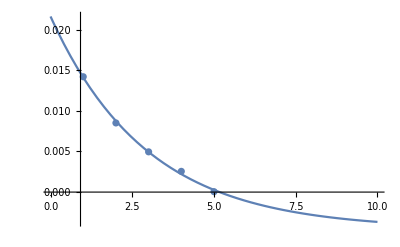

```mathematica
Show[ListPlot[c0l],Plot[ffn3[rs,c0a,c0b,c0c],{rs,0,10}],PlotRange->Full]
```

```mathematica
{c1a,c1b,c1c}={a,b,c}/.FindFit[c1l,ffn2[x,a,b,c],{a,b,c},x]
```

{0.983665,-0.81567,0.984994}

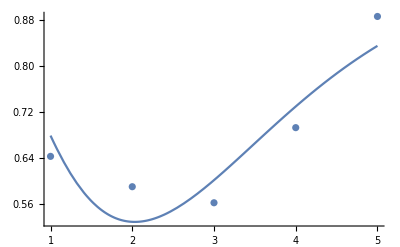

```mathematica
Show[ListPlot[c1l],Plot[ffn2[rs,c1a,c1b,c1c],{rs,1,5}],PlotRange->Full]
```

```mathematica
{c2a,c2b,c2c}={a,b,c}/.FindFit[c2l,ffn2[x,a,b,c],{a,b,c},x]
```

{1.4431,22.0007,3.66798}

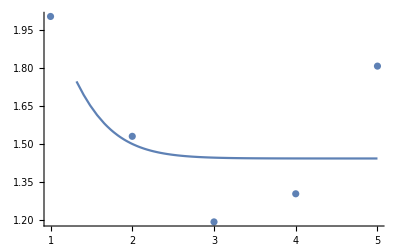

```mathematica
Show[ListPlot[c2l],Plot[ffn2[rs,c2a,c2b,c2c],{rs,1,5}],PlotRange->Full]
```

```mathematica
pdat=Import["/Users/aaronkaplan/Dropbox/phd.nosync/LFF/codes/optpars_gplus.csv","CSV"]
```

{{rs,c0,c1,c2},{1,0.0146633,4.55818,1.1627},{2,0.0106896,4.37278,1.21886},{5,0.00534549,13.7392,1.19224},{10,-0.000295817,219.322,1.24033}}

```mathematica
c0l=Table[{pdat[[i,1]],pdat[[i,2]]},{i,2,Length[pdat]}];
c1l = Table[{pdat[[i,1]],pdat[[i,3]]},{i,2,Length[pdat]}];
c2l = Table[{pdat[[i,1]],pdat[[i,4]]},{i,2,Length[pdat]}];
```

```mathematica
{c0aa,c0bb}={a,b}/.FindFit[c0l,ffn[x,a,b],{a,b},x]
```

{0.0196648,0.29417}

```mathematica
{c0a,c0b,c0c}={a,b,c}/.FindFit[c0l,ffn3[x,a,b,c],{a,b,c},x]
```

{-0.00365479,0.0215642,0.182898}

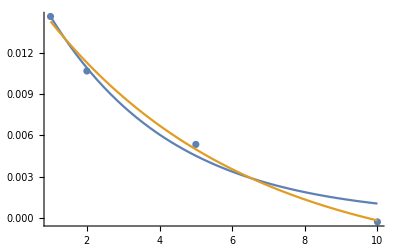

```mathematica
Show[ListPlot[c0l],Plot[{ffn[rs,c0aa,c0bb],ffn3[rs,c0a,c0b,c0c]},{rs,1,10},PlotRange->Full],PlotRange->Full]
```

```mathematica
{c1a,c1b,c1c}={a,b,c}/.FindFit[c1l,ffn[x,a,b],{a,b,c},x]
```

{0.99735,-0.539306,1.}

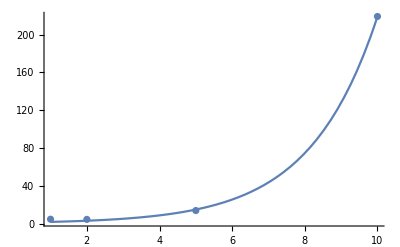

```mathematica
Show[ListPlot[c1l],Plot[ffn[rs,c1a,c1b],{rs,1,10},PlotRange->Full],PlotRange->Full]
```

```mathematica
{c2a,c2b,c2c}={a,b,c}/.FindFit[c2l,ffn3[x,a,b,c],{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.21715,-239.036,8.38715}

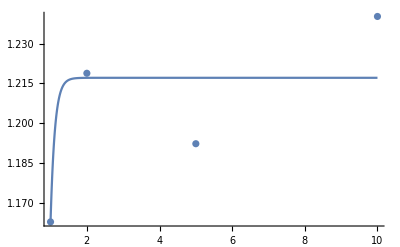

```mathematica
Show[ListPlot[c2l],Plot[ffn3[rs,c2a,c2b,c2c],{rs,1,10},PlotRange->Full],PlotRange->Full]
```